## 2.1a)

-1

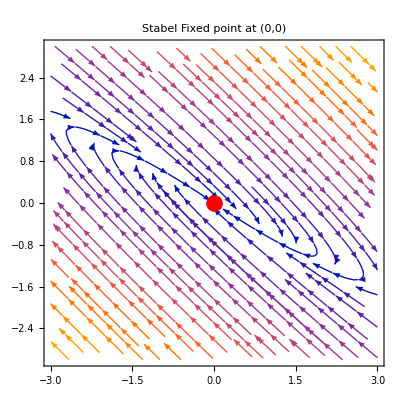

{-1,-1}

```mathematica
sigma=-1
stream=StreamPlot[{(sigma+3)x+4y,(-9/4)x+(sigma-3)y},{x,-3,3},{y,-3,3},PlotLabel->"Stabel Fixed point at (0,0)"];
fp=Graphics[{Red,PointSize[0.03],Point[{0,0}]},Axes->True,AxesOrigin->{0,0}];
Show[stream,fp]
f[x_,y_]:=(2)x+4y
g[x_,y_]:=(-9/4)x+(-4)y

j=D[{f[x,y],g[x,y]},{{x,y}}];
Eigenvalues[j]
```

This is a stabel fixed point at (0,0) because eigenvalues real part negative

0

{0,0}

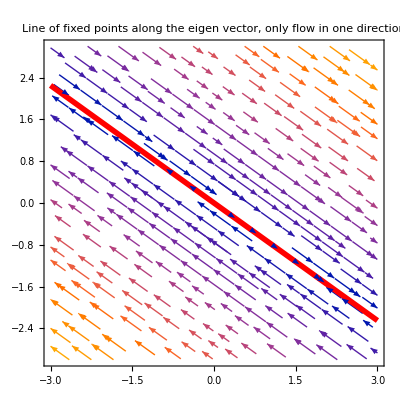

```mathematica
sigma=0
stream = StreamPlot[{(sigma+3)x+4y,(-9/4)x+(sigma-3)y},{x,-3,3},{y,-3,3},PlotLabel->"Line of fixed points along the eigen vector, only flow in one direction"];
f[x_,y_]:=(3)x+4y
g[x_,y_]:=(-9/4)x+(-3)y

j=D[{f[x,y],g[x,y]},{{x,y}}];
Eigenvalues[j]
eVector=Eigenvectors[j];
eVector[[1,2]];
fp=Graphics[{Red,Thickness[0.01],Line[{{-3,-3 eVector[[1,2]]/eVector[[1,1]]},{3,3 eVector[[1,2]]/eVector[[1,1]]}}]}];

Show[stream,fp]
```

Line of fix points

1

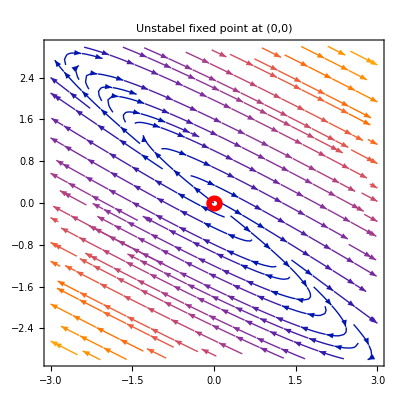

```mathematica
sigma=1
stream=StreamPlot[{(sigma+3)x+4y,(-9/4)x+(sigma-3)y},{x,-3,3},{y,-3,3},PlotLabel->"Unstabel fixed point at (0,0)"];
fp=Graphics[{Red,Thickness[0.01],Circle[{0,0},0.1]}];
Show[stream,fp]
```

```mathematica
f[x_,y_]:=(4)x+4y
g[x_,y_]:=(-9/4)x+(-2)y

j=D[{f[x,y],g[x,y]},{{x,y}}];
Eigenvalues[j]
```

{1,1}

This is a unstable fixed point at (0,0) because eigenvalues real part positive

## 2.1 b)

```mathematica
matrix={{σ+3,4},{-9/4,σ-3}}
```

```mathematica
matrix={{σ+3,4},{-9/4,σ-3}};
```

2.1c)

```mathematica
vectors=Eigenvectors[{{3+σ,4},{-9/4,-3+σ}}]
```

{{-4/3,1},{0,0}}

```mathematica
eigenVector=vectors[[1]]
```

{-4/3,1}

```mathematica
magnitude=Sqrt[Total[eigenVector^2]];
```

```mathematica
normalizedVector=-eigenVector/magnitude
```

{4/5,-3/5}

2.1 d)

```mathematica
Inverse[matrix]
```

{{(-12+4 σ)/(4 σ^2),-4/σ^2},{9/(4 σ^2),(3+σ)/σ^2}}

12.1 e)
when sigma =0 inverse of A goes to inf therefor sigma =0 implies that invers of A dosent excist in this particular case (sigma =0)

2.1 f)

```mathematica
matrixGeneral={{σ-cd,d^2},{-c^2,σ+cd}}
matrixSigmaMinus={{-1-cd,d^2},{-c^2,-1+cd}}
```

{{-cd+σ,d^2},{-c^2,cd+σ}}

{{-1-cd,d^2},{-c^2,-1+cd}}

```mathematica
Eigensystem[matrixSigmaMinus]
```

{{-1-√(cd^2-c^2 d^2),-1+√(cd^2-c^2 d^2)},{{-(-cd-√(cd^2-c^2 d^2))/c^2,1},{-(-cd+√(cd^2-c^2 d^2))/c^2,1}}}

```mathematica
Eigenvalues[matrixSigmaMinus]
```

{-1-√(cd^2-c^2 d^2),-1+√(cd^2-c^2 d^2)}

```mathematica
Eigenvectors[matrixSigmaMinus]
```

{{-(-cd-√(cd^2-c^2 d^2))/c^2,1},{-(-cd+√(cd^2-c^2 d^2))/c^2,1}}

Eigenvalues should be the same as previous [sigma,sigma] (sigma=-1) therfore sqrt(cd^2-c^2d^2)=0 . Given this the eigenvector is [d/c,1].